```mathematica
R=(a-b+c^2)/(a+b+c^2)+(ac^2-b+1)/(ac^2+b+1)
```

(1+ac^2-b)/(1+ac^2+b)+(a-b+c^2)/(a+b+c^2)

```mathematica
Simplify[R]
```

(1+ac^2-b)/(1+ac^2+b)+(a-b+c^2)/(a+b+c^2)

```mathematica
FullSimplify[R]
```

(2 (1+ac^2))/(1+ac^2+b)-(2 b)/(a+b+c^2)

```mathematica
R2=((a-b+c^2)*(ac^2+b+1)+(ac^2-b+1)*(a+b+c^2))/((a+b+c^2)*(ac^2+b+1))
```

((1+ac^2+b) (a-b+c^2)+(1+ac^2-b) (a+b+c^2))/((1+ac^2+b) (a+b+c^2))

```mathematica
Simplify[R2]
```

(2 (a (1+ac^2)-b^2+(1+ac^2) c^2))/((1+ac^2+b) (a+b+c^2))

```mathematica
Den=(a+b+c^2)*(ac^2+b+1)
```

(1+ac^2+b) (a+b+c^2)

```mathematica
FullSimplify[Den]
```

(1+ac^2+b) (a+b+c^2)

From R2’s simplification (output 6), letting g=1+ac^2

```mathematica
R3=(2 (a g-b^2+g c^2))/((g+b) (a+b+c^2))
```

(2 (-b^2+a g+c^2 g))/((a+b+c^2) (b+g))

```mathematica
FullSimplify[R3]
```

2-(2 b)/(a+b+c^2)-(2 b)/(b+g)

```mathematica
a=Cos[0.1];
b=Sin[0.1];
```

0.995004

0.0998334

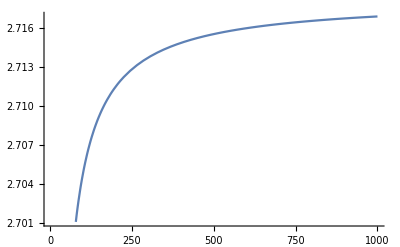

```mathematica
Plot[(1+1/x)^x,{x,1,1000}]
```

```mathematica
Limit[Sin[x]/x,{x-> 0}]
```

{1}